```mathematica
T0= 1
Ti[r] =T0 (1+r^2)/2
```

1/2 (1+r^2)

```mathematica
-eD ϕ''[r] == eD^2
```

```mathematica
eD (ni E^(-Vp / Ti)-nF E^(-Ve / Te))
```

```mathematica
ni E^(-Vp / Ti)-nF E^(-Ve / Te)/.Vp-> mpD ϕg + eD ϕD /.Ve -> -eD ϕD
ϕ0sol=Solve[%==0,ϕD][[1]]
```

-ⅇ^((eD ϕD)/Te) nF+ⅇ^(-(eD ϕD+mpD ϕg)/Ti) ni

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ϕD→-(Te (mpD ϕg+Ti Log[nF/ni]))/(eD (Te+Ti))}

```mathematica
(eD ϕD)/(-mpD ϕg)/.ϕ0sol/.Te->Ti/TibyTe/.mpD -> - Ti/(Tibyϕg ϕg)/.ni->nF/nFbyni//FullSimplify
```

(1-Tibyϕg Log[nFbyni])/(1+TibyTe)

```mathematica
ni E^(-Vp / Ti)-nF E^(-Ve / Te)/.Vp-> mpD ϕg + eD ϕD /.Ve -> -eD ϕD
```

-ⅇ^((eD ϕD)/Te) nF+ⅇ^(-(eD ϕD+mpD ϕg)/Ti) ni

```mathematica
-(1-Tibyϕg Log[nFbyni])/(1+TibyTe)/.TibyTe ->0.01/.Tibyϕg->0.01/.nFbyni->0.5
```

-0.996962

0.990099 (1-0.01 Log[nFbyni])

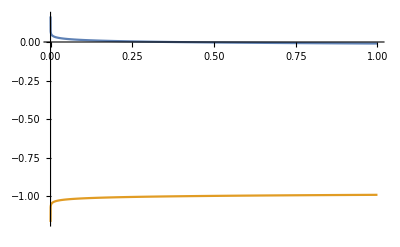

```mathematica
(1-Tibyϕg Log[nFbyni])/(1+TibyTe)/.TibyTe ->0.01/.Tibyϕg->0.01
Plot[{%-1,-%},{nFbyni,0,1}]
```

```mathematica
-ⅇ^((eD ϕD)/Te) nF+ⅇ^(-(eD ϕD+mpD ϕg)/Ti) ni /.ϕ0sol//Simplify

(*/.Te->Ti/TibyTe/.mpD -> - Ti/(Tibyϕg ϕg)/.ni->nF/nFbyni//FullSimplify*)
```

0

Story here is: captured dark protons are colder, as the temperature decreases the relative density and potential increases, a smaller and smaller potential is needed to compensate for the density differrence of the two species.

```mathematica
niT=ⅇ^(-(eD ϕD+mpD ϕg)/Ti) ni
neT=-ⅇ^((eD ϕD)/Te) nF
```

ⅇ^(-(eD ϕD+mpD ϕg)/Ti) ni

-ⅇ^((eD ϕD)/Te) nF

```mathematica
niT Ti[r] ==
```

```mathematica
Solve[ni-ⅇ^((eD ϕD)/Te) nF==0,{ϕD}]
```

{{ϕD→ConditionalExpression[(Te (2 ⅈ π C[1]+Log[ni/nF]))/eD, C[1]∈ℤ]}}